In this notebook we compare the QCD running of α_S in RunDec and DsixTools. DsixTools uses the full 6 flavor QCD beta function at 1 loop, from Mw to Λ, while RunDec uses the correct n_f flavor QCD beta function at 4 loops, from Mw, to Λ. We find that the ratio of the two is less than 2% from Mw to 10 GeV.

```mathematica
Quit[];
```

```mathematica
1+1//Timing
```

{6.×10^-6,2}

```mathematica
<<"/Users/noahsteinberg/Library/Mathematica/Applications/DsixTools/DsixTools.m"
```

DsixTools 1.1.3

by Alejandro Celis, Javier Fuentes-Martin, Avelino Vicente and Javier Virto

Reference: arXiv:1704.04504

Website: https://dsixtools.github.io/

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version.

See ?DsixTools`* for a list of routines and variables.

```mathematica
<<"/Users/noahsteinberg/Desktop/BNV_Mathematica_Programs/RunDec.m"
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (April 2016, v2.1)

```mathematica
(*Here let's run αS from 10TeV down to Mtop at 1 loop, using RunDec*)

Mtop = 173.21;

alphaS4loopRunDecLow[μ_, mt_, MZ_, MW_, as5MZ_] := Module[{as5mw},
as5mw = AlphasExact[as5MZ, MZ, MW, 5, 4];
as5μ = AlphasExact[as5mw, MW, μ, 5, 4];
Return[as5μ];]
alphaS4loopRunDecHigh[μ_, mt_, MZ_, as5MZ_]:= Module[{as5mt, as6mt, as6μ},
as5mt = AlphasExact[as5MZ, MZ, mt, 5, 4];
as6mt = DecAsUpOS[as5mt, mt, mt, 5, 4];
as6μ = AlphasExact[as6mt, mt, μ, 6, 4];
Return[as6μ];]
alphaRunDec[μ_] := 
If[μ ≤ Mtop, alphaS4loopRunDecLow[μ, Mtop, 91.1876, 80.385, .1182], alphaS4loopRunDecHigh[μ, Mtop, 91.1876, .1182]]
```

```mathematica
AlphasExact[.1182,91.1876,80.385, 5,4]
```

0.120502

```mathematica
DecAsUpOS[0.120502,173.21,80.385,5,4]
```

0.119167

```mathematica
alphamw = alphaRunDec[80.385];
```

```mathematica
RunDecPlot = 
Plot[alphaRunDec[10^logMX], {logMX,Log10[80.385], 7}, Frame->True, FrameLabel->{"Log_10(μ/GeV)", "α_s"}, PlotStyle->{Green},  PlotLegends->{"4 loop QCD RunDec"}];
```

### Options

```mathematica
Options
LOWSCALE=mW;
HIGHSCALE=10^7;
CPV=0;
ReadRGEs=1;
RGEsMethod=1;
ExportRGEs=0;
UseRGEsSM=1;
exportSMEFTrunner=0;
exportEWmatcher=0;
exportWETrunner=0;
inputWCsType=1;

Init[g]=e/Sin[θW];
Init[gp]=e/Cos[θW];
Init[gs]=Sqrt[4Pi(alphamw)]; (*We feed as input to DsixTools Subscript[α, s](Subscript[M, Z])*);

Init[λ]=mh^2/v^2;
Init[m2]=mh^2/2;
Init[GU[1,1]]=1.23231*10^-5;
Init[GU[1,2]]=-1.64215*10^-3;
Init[GU[1,3]]=5.90635*10^-3;
Init[GU[2,1]]=2.84527*10^-6;
Init[GU[2,2]]=7.10724*10^-3;
Init[GU[2,3]]=-4.18547*10^-2;
Init[GU[3,1]]=4.65426*10^-8;
Init[GU[3,2]]=3.08758*10^-4;
Init[GU[3,3]]=0.994858;
Init[GD[1,1]]=2.70195*10^-5;
Init[GD[1,2]]=0;
Init[GD[1,3]]=0;
Init[GD[2,1]]=0;
Init[GD[2,2]]=5.51888*10^-4;
Init[GD[2,3]]=0;
Init[GD[3,1]]=0;
Init[GD[3,2]]=0;
Init[GD[3,3]]=2.403012*10^-2;
Init[GE[1,1]]=2.93766*10^-6;
Init[GE[1,2]]=0;
Init[GE[1,3]]=0;
Init[GE[2,1]]=0;
Init[GE[2,2]]=6.07422*10^-4;
Init[GE[2,3]]=0;
Init[GE[3,1]]=0;
Init[GE[3,2]]=0;
Init[GE[3,3]]=1.02157*10^-2;
Init[θ]=0;
Init[θp]=0;
Init[θs]=0;
```

Options

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Example_IO"];
WriteAndReadInputFiles["Options_program2.dat","WCsInput_program2.dat","SMInput_program2.dat"];
```

SetDirectory::cdir: Cannot set current directory to ../Example_IO.

Input : SMEFT Wilson coefficients

```mathematica
(*Now let's run αS from 10 TeV down to Mtop at 1 loop, using DSixTools*)
LoadModule["SMEFTrunner"]
LoadBetaFunctions;
RunRGEsSMEFT;
param1 = FindParameterSMEFT[gs];

DsixTools1loop = 
Plot[outSMEFTrunner[[param1]]^2/(4π), {t, tLOW, tHIGH}, Frame->True, Axes->False, PlotRange->{{tLOW, tHIGH}, Automatic}, PlotLegends->{"1 loop QCD DsixTools"}, PlotStyle->{Red}];
```

LoadModule::Already: Warning : SMEFTrunner module already loaded

Loading SMEFT β functions

Running

Running finished!

```mathematica
(*Now we compare the two*)
```

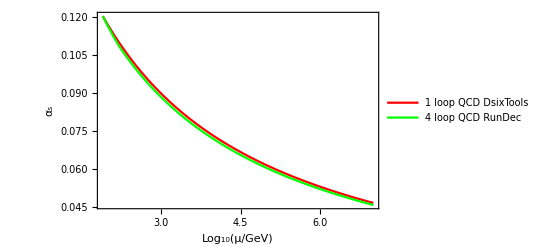

```mathematica
Show[DsixTools1loop, RunDecPlot, PlotRange->All, Frame->True, FrameLabel->{"Log_10(μ/GeV)", "α_s"}]
```

```mathematica
alphaSMEFT[μ_] := outSMEFTrunner[[3]]^2/(4π)/.t->Log10[μ]
```

```mathematica
alphaSMEFT[173.21]
```

0.109244

```mathematica
alphaRunDec[173.21]
```

0.107754

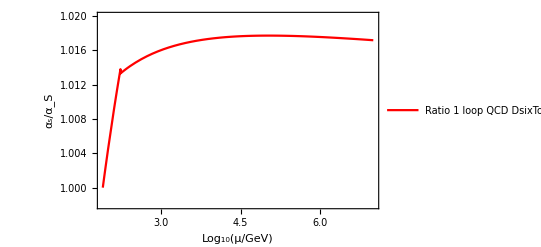

```mathematica
Plot[(outSMEFTrunner[[param1]]^2/(4π))/alphaRunDec[10^t], {t, tLOW, 7}, Frame->True, Axes->False, PlotRange->{{tLOW,7}, {.998,1.02}}, PlotLegends->{"Ratio 1 loop QCD DsixTools to 4 loop RunDec"},FrameLabel->{"Log_10(μ/GeV)", "α_s/α_S"},  PlotStyle->{Red}]
```

```mathematica
alphaRunDec[10^7]
```

0.046007568397716116908